Curva característica I-V y Conductancia G-V de uniones túnel metal-aislante-superconductor 
Unidades: Δ=1(medio gap del superconductor), k=1(cte. de Boltzmann), e=1(carga del electrón)
Parámetros a especificar: 
T: temperatura  
(T en kelvin)=(Δ/k)*(T del programa)
Si el SC es Pb: Δ=1,34 meV----->
----->(T en kelvin)=(15,54 kelvin /unidades del programa)*(T del programa). Esta es la conversión que usa el programa en la tercera línea del código.
vmax: valor máximo del voltaje
paso: tamaño de la discretización del eje de voltajes
El Output es 1.ba I-V y 2.ba G-V
nota: el programa no es válido para temperaturas menores de 0,05 (underflow: aparecen n.bas demasiado pequeños) ni vmax mayor que 5  (¿?)

```mathematica
T=0.05;vmax=5.;paso=0.02;
Int=.;V=. ;g=.;IdeV=.;GdeV=.;
Temp=15.536*T;
Print["T=",Temp,"K"]
f=e/(√(e^2-1))(1/(Exp[e/T]+1)-1/(Exp[(e+V)/T]+1));
Int=Table[NIntegrate[f,{e,1,∞}]-NIntegrate[f,{e,-∞,-1}],{V,paso,vmax,paso}];
G=Table[(Int[[i+1]]-Int[[i]])/paso,{i,(vmax/paso)-1.}];
IdeV=Table[{paso*i,Int[[i]]},{i,vmax/paso}];
GdeV=Table[{paso*i,G[[i]]},{i,(vmax/paso)-1}];
```

T=0.7768K

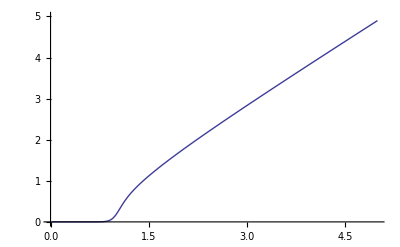

```mathematica
ListPlot[IdeV,PlotJoined->True,PlotRange->{{0.,vmax},{0.,vmax}}]
```

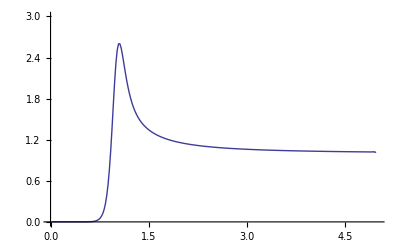

```mathematica
ListPlot[GdeV,PlotJoined->True,PlotRange->{{0.,vmax},{0.,3.}}]
```

```mathematica
(*PARA GRABAR LOS DATOS EN UN FICHERO DE FORMATO .DAT *)
Export["/Users/dd46mi/desktop/universidad/TRABAJOS/tecnicas_experimentales_IV_UAM/programa_Mathematica/simulaciones_graficas/simulacion_iv.txt",Re[IdeV],"Table"]
Export["/Users/dd46mi/desktop/universidad/TRABAJOS/tecnicas_experimentales_IV_UAM/programa_Mathematica/simulaciones_graficas/simulacion_gv.txt",Re[GdeV],"Table"]
```

/Users/dd46mi/desktop/universidad/TRABAJOS/tecnicas_experimentales_IV_UAM/programa_Mathematica/simulaciones_graficas/iv.txt

/Users/dd46mi/desktop/universidad/TRABAJOS/tecnicas_experimentales_IV_UAM/programa_Mathematica/simulaciones_graficas/gv.txt